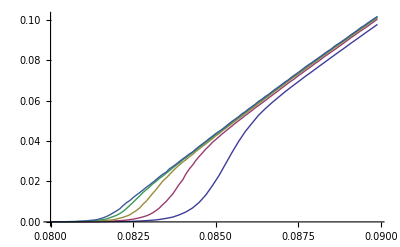

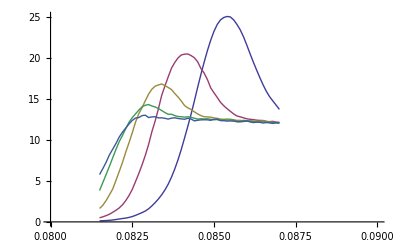

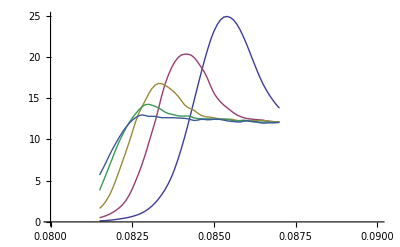

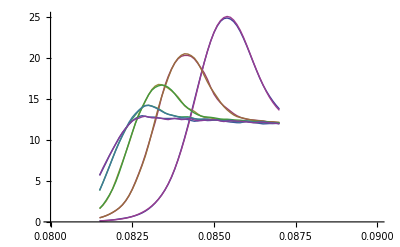

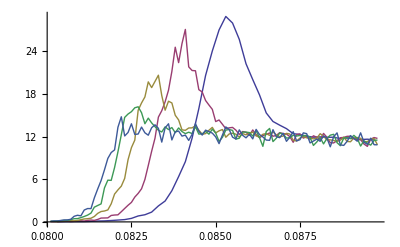

```mathematica
ListPlot[{Gap[v][5],Gap[v][10],Gap[v][20],Gap[v][40],Gap[v][80]},Joined->True]
ListLinePlot[{dgdd1[v][5],dgdd1[v][10],dgdd1[v][20],dgdd1[v][40],dgdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dg1dd1[v][5],dg1dd1[v][10],dg1dd1[v][20],dg1dd1[v][40],dg1dd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dg1dd1[v][5],dg1dd1[v][10],dg1dd1[v][20],dg1dd1[v][40],dg1dd1[v][80],dg2dd1[v][5],dg2dd1[v][10],dg2dd1[v][20],dg2dd1[v][40],dg2dd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dgdd[v][5],dgdd[v][10],dgdd[v][20],dgdd[v][40],dgdd[v][80]}]
```

```mathematica
p=0.1;
Do[
AVeldif0[v][l]=Table[{AVel[v][l][[All,1]][[i]],v*(1-p)+(v-1)*p-AVel[v][l][[All,2]][[i]]},{i,1,Length[AVel[v][l]]}];
,{l,{5,10,20,40,80}}]
```

```mathematica
Do[
sVel[v][l]=Table[{AVel[v][l][[All,1]][[i]],(v-3)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p^2)+(v-2)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p^2)+(v-1)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p(1-p))+v(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))(1-p)},{i,1,Length[AVel[v][l]]}];

sVar[v][l]=Table[{AVVar[v][l][[All,1]][[i]],(v-3)^2*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p^2)+(v-2)^2*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p^2)+(v-1)^2*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p(1-p))+v^2*(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))(1-p)-((v-3)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p^2)+(v-2)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p^2)+(v-1)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p(1-p))+v(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))(1-p))^2},{i,1,Length[AVVar[v][l]]}];



AVeldif[v][l]=Table[{AVel[v][l][[All,1]][[i]],sVel[v][l][[All,2]][[i]]-AVel[v][l][[All,2]][[i]]},{i,1,Length[AVel[v][l]]}];

Vardif[v][l]=Table[{AVVar[v][l][[All,1]][[i]],AVVar[v][l][[All,2]][[i]]-sVar[v][l][[All,2]][[i]]},{i,1,Length[AVel[v][l]]}];


,{l,{5,10,20,40,80}}]
```

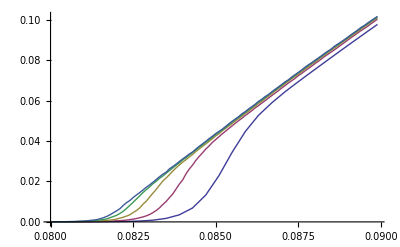

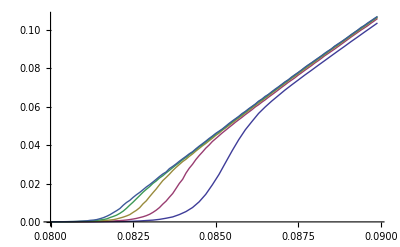

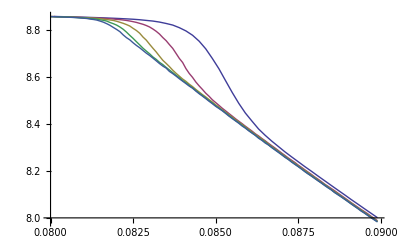

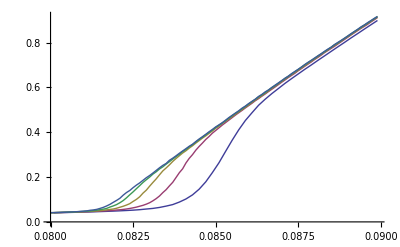

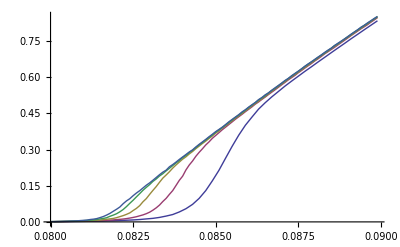

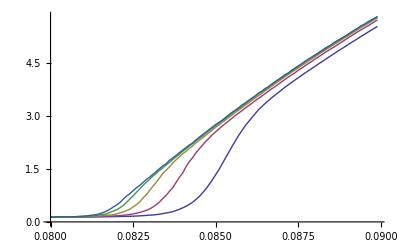

```mathematica
ListPlot[{Gap[v][5],Gap[v][10],Gap[v][20],Gap[v][40],Gap[v][80]},Joined->True]
ListPlot[{Vel[v][5],Vel[v][10],Vel[v][20],Vel[v][40],Vel[v][80]},Joined->True]
ListPlot[{AVel[v][5],AVel[v][10],AVel[v][20],AVel[v][40],AVel[v][80]},Joined->True]
ListPlot[{AVeldif0[v][5],AVeldif0[v][10],AVeldif0[v][20],AVeldif0[v][40],AVeldif0[v][80]},Joined->True]
ListPlot[{AVeldif[v][5],AVeldif[v][10],AVeldif[v][20],AVeldif[v][40],AVeldif[v][80]},Joined->True]
ListPlot[{AVVar[v][5],AVVar[v][10],AVVar[v][20],AVVar[v][40],AVVar[v][80]},Joined->True]
```

```mathematica
δ=0.00075;
Do[

ig[v][l]=Interpolation[Gap[v][l]];
iv[v][l]=Interpolation[Vel[v][l]];
iav[v][l]=Interpolation[AVel[v][l]];
iavd0[v][l]=Interpolation[AVeldif0[v][l]];
iavd[v][l]=Interpolation[AVeldif[v][l]];
ivar[v][l]=Interpolation[AVVar[v][l]];
ivardif[v][l]=Interpolation[Vardif[v][l]];


dgdd1[v][l]=Table[{x,(ig[v][l][x+δ]-ig[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
dvdd1[v][l]=Table[{x,(iv[v][l][x+δ]-iv[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
davdd1[v][l]=Table[{x,(iav[v][l][x+δ]-iav[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
davdif0dd1[v][l]=Table[{x,(iavd0[v][l][x+δ]-iavd0[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
davdifdd1[v][l]=Table[{x,(iavd[v][l][x+δ]-iavd[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
dvardd1[v][l]=Table[{x,(ivar[v][l][x+δ]-ivar[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];
dvardifdd1[v][l]=Table[{x,(ivardif[v][l][x+δ]-ivardif[v][l][x-δ])/(2*δ)},{x,0.0812,0.089,0.0001}];

dgdd[v][l]=Table[{Gap[v][l][[All,1]][[i]],(Gap[v][l][[All,2]][[i+1]]-Gap[v][l][[All,2]][[i-1]])/(Gap[v][l][[All,1]][[i+1]]-Gap[v][l][[All,1]][[i-1]])},{i,2,Length[Gap[v][l]]-1}];
dvdd[v][l]=Table[{Vel[v][l][[All,1]][[i]],(Vel[v][l][[All,2]][[i+1]]-Vel[v][l][[All,2]][[i-1]])/(Vel[v][l][[All,1]][[i+1]]-Vel[v][l][[All,1]][[i-1]])},{i,2,Length[Vel[v][l]]-1}];
davdd[v][l]=Table[{AVel[v][l][[All,1]][[i]],(AVel[v][l][[All,2]][[i+1]]-AVel[v][l][[All,2]][[i-1]])/(AVel[v][l][[All,1]][[i+1]]-AVel[v][l][[All,1]][[i-1]])},{i,2,Length[AVel[v][l]]-1}];
davdif0dd[v][l]=Table[{AVeldif0[v][l][[All,1]][[i]],(AVeldif0[v][l][[All,2]][[i+1]]-AVeldif0[v][l][[All,2]][[i-1]])/(AVeldif0[v][l][[All,1]][[i+1]]-AVeldif0[v][l][[All,1]][[i-1]])},{i,2,Length[AVeldif0[v][l]]-1}];
davdifdd[v][l]=Table[{AVeldif[v][l][[All,1]][[i]],(AVeldif[v][l][[All,2]][[i+1]]-AVeldif[v][l][[All,2]][[i-1]])/(AVeldif[v][l][[All,1]][[i+1]]-AVeldif[v][l][[All,1]][[i-1]])},{i,2,Length[AVeldif[v][l]]-1}];
dvardd[v][l]=Table[{AVVar[v][l][[All,1]][[i]],(AVVar[v][l][[All,2]][[i+1]]-AVVar[v][l][[All,2]][[i-1]])/(AVVar[v][l][[All,1]][[i+1]]-AVVar[v][l][[All,1]][[i-1]])},{i,2,Length[AVVar[v][l]]-1}];

dvardifdd[v][l]=Table[{Vardif[v][l][[All,1]][[i]],(Vardif[v][l][[All,2]][[i+1]]-Vardif[v][l][[All,2]][[i-1]])/(Vardif[v][l][[All,1]][[i+1]]-Vardif[v][l][[All,1]][[i-1]])},{i,2,Length[Vardif[v][l]]-1}];


,{l,{5,10,20,40,80}}]
```

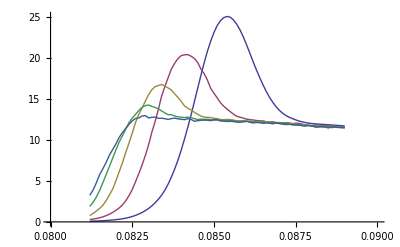

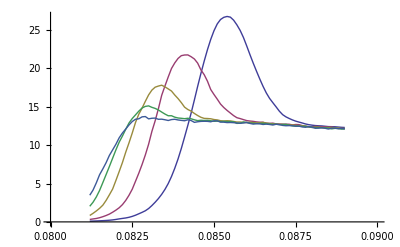

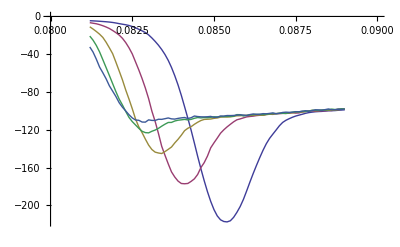

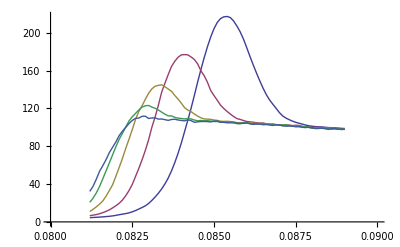

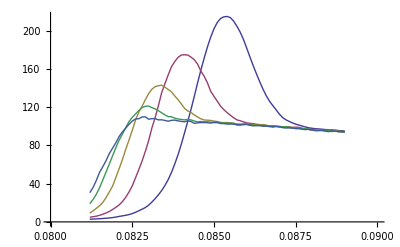

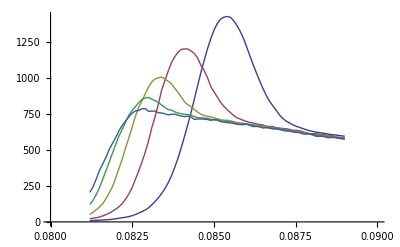

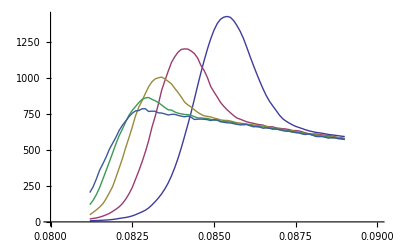

```mathematica
ListLinePlot[{dgdd1[v][5],dgdd1[v][10],dgdd1[v][20],dgdd1[v][40],dgdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvdd1[v][5],dvdd1[v][10],dvdd1[v][20],dvdd1[v][40],dvdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdd1[v][5],davdd1[v][10],davdd1[v][20],davdd1[v][40],davdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdif0dd1[v][5],davdif0dd1[v][10],davdif0dd1[v][20],davdif0dd1[v][40],davdif0dd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdifdd1[v][5],davdifdd1[v][10],davdifdd1[v][20],davdifdd1[v][40],davdifdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvardd1[v][5],dvardd1[v][10],dvardd1[v][20],dvardd1[v][40],dvardd1[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvardifdd1[v][5],dvardifdd1[v][10],dvardifdd1[v][20],dvardifdd1[v][40],dvardifdd1[v][80]},PlotRange->{{0.08,0.09},Full}]
```

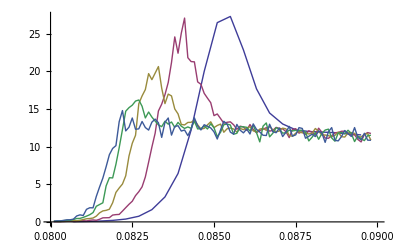

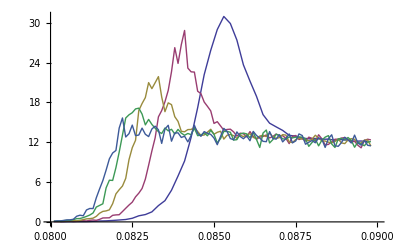

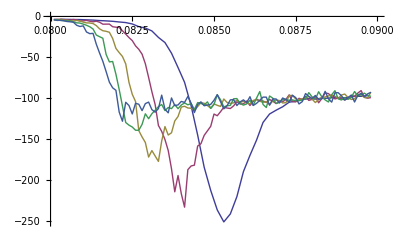

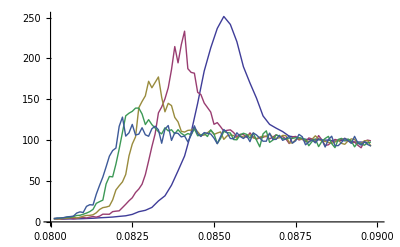

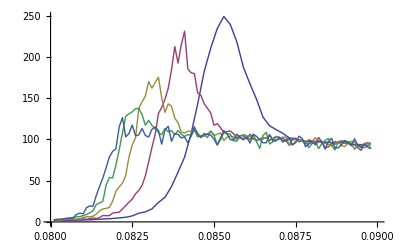

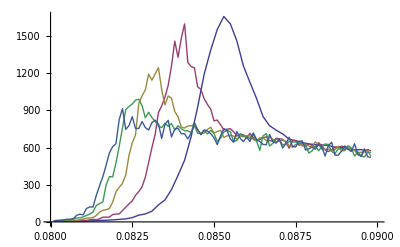

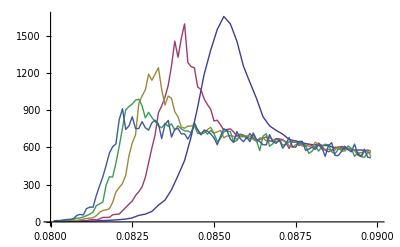

```mathematica
ListLinePlot[{dgdd[v][5],dgdd[v][10],dgdd[v][20],dgdd[v][40],dgdd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvdd[v][5],dvdd[v][10],dvdd[v][20],dvdd[v][40],dvdd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdd[v][5],davdd[v][10],davdd[v][20],davdd[v][40],davdd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdif0dd[v][5],davdif0dd[v][10],davdif0dd[v][20],davdif0dd[v][40],davdif0dd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{davdifdd[v][5],davdifdd[v][10],davdifdd[v][20],davdifdd[v][40],davdifdd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvardd[v][5],dvardd[v][10],dvardd[v][20],dvardd[v][40],dvardd[v][80]},PlotRange->{{0.08,0.09},Full}]
ListLinePlot[{dvardifdd[v][5],dvardifdd[v][10],dvardifdd[v][20],dvardifdd[v][40],dvardifdd[v][80]},PlotRange->{{0.08,0.09},Full}]
```

```mathematica
maxdgdd1[v]=Table[{l*1000,Max[dgdd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdgdd1[v]=Table[{Log[maxdgdd1[v][[All,1]][[i]]],Log[maxdgdd1[v][[All,2]][[i]]]},{i,1,Length[maxdgdd1[v]]}]
pmaxdgdd1[v]=Table[{maxdgdd1[v][[All,1]][[i]],Select[dgdd1[v][maxdgdd1[v][[All,1]][[i]]/1000],#[[2]]==maxdgdd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdgdd1[v]]}]
vvpmaxdgdd1[v]=Table[{pmaxdgdd1[v][[All,1]][[i]],ig[v][pmaxdgdd1[v][[All,1]][[i]]/1000][pmaxdgdd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdgdd1[v]]}]
Logvvpmaxdgdd1[v]=Table[{Log[vvpmaxdgdd1[v][[All,1]][[i]]],Log[vvpmaxdgdd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdgdd1[v]]}]


maxdvdd1[v]=Table[{l*1000,Max[dvdd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdvdd1[v]=Table[{Log[maxdvdd1[v][[All,1]][[i]]],Log[maxdvdd1[v][[All,2]][[i]]]},{i,1,Length[maxdvdd1[v]]}]
pmaxdvdd1[v]=Table[{maxdvdd1[v][[All,1]][[i]],Select[dvdd1[v][maxdvdd1[v][[All,1]][[i]]/1000],#[[2]]==maxdvdd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvdd1[v]]}]
vvpmaxdvdd1[v]=Table[{pmaxdvdd1[v][[All,1]][[i]],iv[v][pmaxdvdd1[v][[All,1]][[i]]/1000][pmaxdvdd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdvdd1[v]]}]
Logvvpmaxdvdd1[v]=Table[{Log[vvpmaxdvdd1[v][[All,1]][[i]]],Log[vvpmaxdvdd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvdd1[v]]}]


maxdavdd1[v]=Table[{l*1000,-Min[davdd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdavdd1[v]=Table[{Log[maxdavdd1[v][[All,1]][[i]]],Log[maxdavdd1[v][[All,2]][[i]]]},{i,1,Length[maxdavdd1[v]]}]
pmaxdavdd1[v]=Table[{maxdavdd1[v][[All,1]][[i]],Select[davdd1[v][maxdavdd1[v][[All,1]][[i]]/1000],#[[2]]==-maxdavdd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdavdd1[v]]}]
vvpmaxdavdd1[v]=Table[{pmaxdavdd1[v][[All,1]][[i]],iav[v][pmaxdavdd1[v][[All,1]][[i]]/1000][pmaxdavdd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdavdd1[v]]}]
Logvvpmaxdavdd1[v]=Table[{Log[vvpmaxdavdd1[v][[All,1]][[i]]],Log[vvpmaxdavdd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdavdd1[v]]}]


maxdavdifdd1[v]=Table[{l*1000,Max[davdifdd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdavdifdd1[v]=Table[{Log[maxdavdifdd1[v][[All,1]][[i]]],Log[maxdavdifdd1[v][[All,2]][[i]]]},{i,1,Length[maxdavdifdd1[v]]}]
pmaxdavdifdd1[v]=Table[{maxdavdifdd1[v][[All,1]][[i]],Select[davdifdd1[v][maxdavdifdd1[v][[All,1]][[i]]/1000],#[[2]]==maxdavdifdd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdavdifdd1[v]]}]
vvpmaxdavdifdd1[v]=Table[{pmaxdavdifdd1[v][[All,1]][[i]],iavd[v][pmaxdavdifdd1[v][[All,1]][[i]]/1000][pmaxdavdifdd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdavdifdd1[v]]}]
Logvvpmaxdavdifdd1[v]=Table[{Log[vvpmaxdavdifdd1[v][[All,1]][[i]]],Log[vvpmaxdavdifdd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdavdifdd1[v]]}]


maxdavdif0dd1[v]=Table[{l*1000,Max[davdif0dd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdavdif0dd1[v]=Table[{Log[maxdavdif0dd1[v][[All,1]][[i]]],Log[maxdavdif0dd1[v][[All,2]][[i]]]},{i,1,Length[maxdavdif0dd1[v]]}]
pmaxdavdif0dd1[v]=Table[{maxdavdif0dd1[v][[All,1]][[i]],Select[davdif0dd1[v][maxdavdif0dd1[v][[All,1]][[i]]/1000],#[[2]]==maxdavdif0dd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdavdif0dd1[v]]}]
vvpmaxdavdif0dd1[v]=Table[{pmaxdavdif0dd1[v][[All,1]][[i]],iavd0[v][pmaxdavdif0dd1[v][[All,1]][[i]]/1000][pmaxdavdif0dd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdavdif0dd1[v]]}]
Logvvpmaxdavdif0dd1[v]=Table[{Log[vvpmaxdavdif0dd1[v][[All,1]][[i]]],Log[vvpmaxdavdif0dd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdavdif0dd1[v]]}]



maxdvardd1[v]=Table[{l*1000,Max[dvardd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdvardd1[v]=Table[{Log[maxdvardd1[v][[All,1]][[i]]],Log[maxdvardd1[v][[All,2]][[i]]]},{i,1,Length[maxdvardd1[v]]}]
pmaxdvardd1[v]=Table[{maxdvardd1[v][[All,1]][[i]],Select[dvardd1[v][maxdvardd1[v][[All,1]][[i]]/1000],#[[2]]==maxdvardd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvardd1[v]]}]
vvpmaxdvardd1[v]=Table[{pmaxdvardd1[v][[All,1]][[i]],ivar[v][pmaxdvardd1[v][[All,1]][[i]]/1000][pmaxdvardd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdvardd1[v]]}]
Logvvpmaxdvardd1[v]=Table[{Log[vvpmaxdvardd1[v][[All,1]][[i]]],Log[vvpmaxdvardd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvardd1[v]]}]

maxdvardifdd1[v]=Table[{l*1000,Max[dvardifdd1[v][l][[All,2]]]},{l,{5,10,20,40,80}}]
Logmaxdvardifdd1[v]=Table[{Log[maxdvardifdd1[v][[All,1]][[i]]],Log[maxdvardifdd1[v][[All,2]][[i]]]},{i,1,Length[maxdvardifdd1[v]]}]
pmaxdvardifdd1[v]=Table[{maxdvardifdd1[v][[All,1]][[i]],Select[dvardifdd1[v][maxdvardifdd1[v][[All,1]][[i]]/1000],#[[2]]==maxdvardifdd1[v][[All,2]][[i]]&][[All,1]][[1]]},{i,1,Length[maxdvardifdd1[v]]}]
vvpmaxdvardifdd1[v]=Table[{pmaxdvardifdd1[v][[All,1]][[i]],ivardif[v][pmaxdvardifdd1[v][[All,1]][[i]]/1000][pmaxdvardifdd1[v][[All,2]][[i]]]},{i,1,Length[pmaxdvardifdd1[v]]}]
Logvvpmaxdvardifdd1[v]=Table[{Log[vvpmaxdvardifdd1[v][[All,1]][[i]]],Log[vvpmaxdvardifdd1[v][[All,2]][[i]]]},{i,1,Length[vvpmaxdvardifdd1[v]]}]
```

{{5000,25.1178},{10000,20.4552},{20000,16.7979},{40000,14.2906},{80000,12.9912}}

{{Log[5000],3.22358},{Log[10000],3.01824},{Log[20000],2.82125},{Log[40000],2.6596},{Log[80000],2.56427}}

{{5000,0.0854},{10000,0.0842},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0315482},{10000,0.026113},{20000,0.0201825},{40000,0.0172845},{80000,0.0171384}}

{{Log[5000],-3.45624},{Log[10000],-3.64532},{Log[20000],-3.90294},{Log[40000],-4.05795},{Log[80000],-4.06643}}

{{5000,26.764},{10000,21.7538},{20000,17.8087},{40000,15.1142},{80000,13.7235}}

{{Log[5000],3.28706},{Log[10000],3.07979},{Log[20000],2.87969},{Log[40000],2.71564},{Log[80000],2.61911}}

{{5000,0.0854},{10000,0.0842},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0340457},{10000,0.0279711},{20000,0.0215394},{40000,0.0183942},{80000,0.0182}}

{{Log[5000],-3.38005},{Log[10000],-3.57658},{Log[20000],-3.83787},{Log[40000],-3.99572},{Log[80000],-4.00633}}

{{5000,217.352},{10000,177.004},{20000,145.038},{40000,123.152},{80000,111.819}}

{{Log[5000],5.38152},{Log[10000],5.17617},{Log[20000],4.977},{Log[40000],4.81342},{Log[80000],4.71688}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,8.56024},{10000,8.63705},{20000,8.67242},{40000,8.70011},{80000,8.70283}}

{{Log[5000],2.14713},{Log[10000],2.15606},{Log[20000],2.16015},{Log[40000],2.16334},{Log[80000],2.16365}}

{{5000,214.821},{10000,174.775},{20000,142.95},{40000,121.138},{80000,109.823}}

{{Log[5000],5.3698},{Log[10000],5.1635},{Log[20000],4.96249},{Log[40000],4.79693},{Log[80000],4.69887}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.289024},{10000,0.2153},{20000,0.181439},{40000,0.154569},{80000,0.152055}}

{{Log[5000],-1.24125},{Log[10000],-1.53573},{Log[20000],-1.70684},{Log[40000],-1.86711},{Log[80000],-1.88351}}

{{5000,217.352},{10000,177.004},{20000,145.038},{40000,123.152},{80000,111.819}}

{{Log[5000],5.38152},{Log[10000],5.17617},{Log[20000],4.977},{Log[40000],4.81342},{Log[80000],4.71688}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.339755},{10000,0.262947},{20000,0.227577},{40000,0.199889},{80000,0.197174}}

{{Log[5000],-1.07953},{Log[10000],-1.3358},{Log[20000],-1.48026},{Log[40000],-1.61},{Log[80000],-1.62367}}

{{5000,1429.91},{10000,1204.11},{20000,1008.29},{40000,866.259},{80000,788.145}}

{{Log[5000],7.26537},{Log[10000],7.0935},{Log[20000],6.91601},{Log[40000],6.76418},{Log[80000],6.66968}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,1.97845},{10000,1.55809},{20000,1.36771},{40000,1.20206},{80000,1.1968}}

{{Log[5000],0.682315},{Log[10000],0.443459},{Log[20000],0.31314},{Log[40000],0.184037},{Log[80000],0.179651}}

{{5000,1427.59},{10000,1202.05},{20000,1006.35},{40000,864.387},{80000,786.289}}

{{Log[5000],7.26374},{Log[10000],7.09178},{Log[20000],6.91409},{Log[40000],6.76202},{Log[80000],6.66732}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,1.82148},{10000,1.40396},{20000,1.21498},{40000,1.05009},{80000,1.04501}}

{{Log[5000],0.599649},{Log[10000],0.339295},{Log[20000],0.194727},{Log[40000],0.0488742},{Log[80000],0.0440307}}

```mathematica
Logvvpmaxdgdd1[v]
Logvvpmaxdvdd1[v]
Logvvpmaxdavdd1[v]
Logvvpmaxdavdif0dd1[v]
Logvvpmaxdavdifdd1[v]
Logvvpmaxdvardd1[v]
```

{{Log[5000],-3.45624},{Log[10000],-3.64532},{Log[20000],-3.90294},{Log[40000],-4.05795},{Log[80000],-4.06643}}

{{Log[5000],-3.38005},{Log[10000],-3.57658},{Log[20000],-3.83787},{Log[40000],-3.99572},{Log[80000],-4.00633}}

{{Log[5000],2.14713},{Log[10000],2.15606},{Log[20000],2.16015},{Log[40000],2.16334},{Log[80000],2.16365}}

{{Log[5000],-1.07953},{Log[10000],-1.3358},{Log[20000],-1.48026},{Log[40000],-1.61},{Log[80000],-1.62367}}

{{Log[5000],-1.24125},{Log[10000],-1.53573},{Log[20000],-1.70684},{Log[40000],-1.86711},{Log[80000],-1.88351}}

{{Log[5000],0.682315},{Log[10000],0.443459},{Log[20000],0.31314},{Log[40000],0.184037},{Log[80000],0.179651}}

```mathematica
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0,x]
model1=a0*x-b0;
model2=k0+c0*x^(-ex0)

nlfg1=NonlinearModelFit[Logvvpmaxdgdd1[v],model1,{a0,b0},x];
nlfg1[{"BestFit","ParameterTable"}]

nlfv1=NonlinearModelFit[Logvvpmaxdvdd1[v],model1,{a0,b0},x];
nlfv1[{"BestFit","ParameterTable"}]

nlfav1=NonlinearModelFit[Logvvpmaxdavdd1[v],model1,{a0,b0},x];
nlfav1[{"BestFit","ParameterTable"}]

nlfavdif01=NonlinearModelFit[Logvvpmaxdavdif0dd1[v],model1,{a0,b0},x];
nlfavdif01[{"BestFit","ParameterTable"}]

nlfavdif1=NonlinearModelFit[Logvvpmaxdavdifdd1[v],model1,{a0,b0},x];
nlfavdif1[{"BestFit","ParameterTable"}]

nlfvar1=NonlinearModelFit[Logvvpmaxdvardd1[v],model1,{a0,b0},x];
nlfvar1[{"BestFit","ParameterTable"}]

nlfvardif1=NonlinearModelFit[Logvvpmaxdvardifdd1[v],model1,{a0,b0},x];
nlfvardif1[{"BestFit","ParameterTable"}]
```

0.08122+c0 x^-ex0

{-1.49258-0.235594 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.235594 | 0.0374562 | -6.28984 | 0.00811671
b0 | 1.49258 | 0.37276 | 4.00412 | 0.0279331}

{-1.37083-0.241176 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.241176 | 0.0380333 | -6.34116 | 0.00793207
b0 | 1.37083 | 0.378503 | 3.62172 | 0.0362036}

{2.10047+0.00581585 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 0.00581585 | 0.00130095 | 4.47045 | 0.0208563
b0 | -2.10047 | 0.0129469 | -162.236 | 5.16376×10^-7}

{0.520804-0.196563 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.196563 | 0.035745 | -5.49903 | 0.0118354
b0 | -0.520804 | 0.35573 | -1.46404 | 0.239394}

{0.661891-0.233128 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.233128 | 0.040692 | -5.72908 | 0.0105565
b0 | -0.661891 | 0.404962 | -1.63445 | 0.200676}

{2.16756-0.182465 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.182465 | 0.0339124 | -5.38046 | 0.0125741
b0 | -2.16756 | 0.337493 | -6.42253 | 0.00765051}

{2.24796-0.202216 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | -0.202216 | 0.0368607 | -5.48596 | 0.011914
b0 | -2.24796 | 0.366834 | -6.12802 | 0.00873713}

```mathematica
pmaxdgdd1[v]
pmaxdvdd1[v]
pmaxdavdd1[v]
pmaxdavdif0dd1[v]
pmaxdavdifdd1[v]
pmaxdvardd1[v]
pmaxdvardifdd1[v]
```

{{5000,0.0854},{10000,0.0842},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0854},{10000,0.0842},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

{{5000,0.0854},{10000,0.0841},{20000,0.0834},{40000,0.083},{80000,0.0829}}

«2 more identical outputs»

```mathematica
nlfg2=NonlinearModelFit[pmaxdgdd1[v],model2,{c0,ex0},x];
nlfg2[{"BestFit","ParameterTable"}]

nlfv2=NonlinearModelFit[pmaxdvdd1[v],model2,{c0,ex0},x];
nlfv2[{"BestFit","ParameterTable"}]

nlfav2=NonlinearModelFit[pmaxdavdd1[v],model2,{c0,ex0},x];
nlfav2[{"BestFit","ParameterTable"}]

nlfavdif02=NonlinearModelFit[pmaxdavdif0dd1[v],model2,{c0,ex0},x];
nlfavdif02[{"BestFit","ParameterTable"}]


nlfavdif2=NonlinearModelFit[pmaxdavdifdd1[v],model2,{c0,ex0},x];
nlfavdif2[{"BestFit","ParameterTable"}]

nlfvar2=NonlinearModelFit[pmaxdvardd1[v],model2,{c0,ex0},x];
nlfvar2[{"BestFit","ParameterTable"}]

nlfvardif2=NonlinearModelFit[pmaxdvardifdd1[v],model2,{c0,ex0},x];
nlfvardif2[{"BestFit","ParameterTable"}]
```

{0.08122+0.1056/x^0.382985, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.1056 | 0.0439995 | 2.40003 | 0.0958715
ex0 | 0.382985 | 0.0448909 | 8.53147 | 0.00338318}

{0.08122+0.1056/x^0.382985, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.1056 | 0.0439995 | 2.40003 | 0.0958715
ex0 | 0.382985 | 0.0448909 | 8.53147 | 0.00338318}

{0.08122+0.104276/x^0.382532, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.104276 | 0.0481387 | 2.16616 | 0.118885
ex0 | 0.382532 | 0.0497342 | 7.69153 | 0.00456685}

{0.08122+0.104276/x^0.382532, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.104276 | 0.0481387 | 2.16616 | 0.118885
ex0 | 0.382532 | 0.0497342 | 7.69153 | 0.00456685}

{0.08122+0.104276/x^0.382532, | Estimate | Standard Error | t-Statistic | P-Value
c0 | 0.104276 | 0.0481387 | 2.16616 | 0.118885
ex0 | 0.382532 | 0.0497342 | 7.69153 | 0.00456685}

«2 more identical outputs»

```mathematica
kg=k0;
kv=k0;
kav=k0;
kavdif0=k0;
kavdif=k0;
kvar=k0;
kvardif=k0;

ag=nlfg1["ParameterTableEntries"][[1]][[1]];
cg=nlfg2["ParameterTableEntries"][[1]][[1]];
exg=-nlfg2["ParameterTableEntries"][[2]][[1]];

av=nlfv1["ParameterTableEntries"][[1]][[1]];
cv=nlfv2["ParameterTableEntries"][[1]][[1]];
exv=-nlfv2["ParameterTableEntries"][[2]][[1]];

aav=nlfav1["ParameterTableEntries"][[1]][[1]];
cav=nlfav2["ParameterTableEntries"][[1]][[1]];
exav=-nlfav2["ParameterTableEntries"][[2]][[1]];

aavdif=nlfavdif1["ParameterTableEntries"][[1]][[1]];
cavdif=nlfavdif2["ParameterTableEntries"][[1]][[1]];
exavdif=-nlfavdif2["ParameterTableEntries"][[2]][[1]];

aavdif0=nlfavdif01["ParameterTableEntries"][[1]][[1]];
cavdif0=nlfavdif02["ParameterTableEntries"][[1]][[1]];
exavdif0=-nlfavdif02["ParameterTableEntries"][[2]][[1]];

avar=nlfvar1["ParameterTableEntries"][[1]][[1]];
cvar=nlfvar2["ParameterTableEntries"][[1]][[1]];
exvar=-nlfvar2["ParameterTableEntries"][[2]][[1]];

avardif=nlfvardif1["ParameterTableEntries"][[1]][[1]];
cvardif=nlfvardif2["ParameterTableEntries"][[1]][[1]];
exvardif=-nlfvardif2["ParameterTableEntries"][[2]][[1]];
```

```mathematica
l1=5;
l2=10;
l3=20;
l4=80;
l5=40;
Do[

inputg[l]=Table[{(Gap[v][l][[All,1]][[i]]-(kg+cg*(l*1000)^(exg))),Gap[v][l][[All,2]][[i]]*(l*1000)^(-ag)},{i,1,Length[Gap[v][l]]}];
inputv[l]=Table[{(Vel[v][l][[All,1]][[i]]-(kv+cv*(l*1000)^(exv))),Vel[v][l][[All,2]][[i]]*(l*1000)^(-av)},{i,1,Length[Vel[v][l]]}];
inputav[l]=Table[{(AVel[v][l][[All,1]][[i]]-(kav+cav*(l*1000)^(exav))),AVel[v][l][[All,2]][[i]]*(l*1000)^(-aav)},{i,1,Length[AVel[v][l]]}];
inputavdif0[l]=Table[{(AVeldif0[v][l][[All,1]][[i]]-(kavdif0+cavdif0*(l*1000)^(exavdif0))),AVeldif0[v][l][[All,2]][[i]]*(l*1000)^(-aavdif0)},{i,1,Length[AVeldif0[v][l]]}];
inputavdif[l]=Table[{(AVeldif[v][l][[All,1]][[i]]-(kavdif+cavdif*(l*1000)^(exavdif))),AVeldif[v][l][[All,2]][[i]]*(l*1000)^(-aavdif)},{i,1,Length[AVeldif[v][l]]}];
inputvar[l]=Table[{(AVVar[v][l][[All,1]][[i]]-(kvar+cvar*(l*1000)^(exvar))),AVVar[v][l][[All,2]][[i]]*(l*1000)^(-avar)},{i,1,Length[AVVar[v][l]]}];
inputvardif[l]=Table[{(Vardif[v][l][[All,1]][[i]]-(kvardif+cvardif*(l*1000)^(exvardif))),Vardif[v][l][[All,2]][[i]]*(l*1000)^(-avardif)},{i,1,Length[Vardif[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputg[l][[All,1]][[i]])*(l*1000)^z,inputg[l][[All,2]][[i]]},{i,1,Length[inputg[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zg=z;

]
]

aux
"= zg"zg
```

0.0298

0.13 = zf

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputv[l][[All,1]][[i]])*(l*1000)^z,inputv[l][[All,2]][[i]]},{i,1,Length[inputv[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zv=z;

]
]

aux
"= zv"zv
```

0.0293506

0.12 = zv

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputav[l][[All,1]][[i]])*(l*1000)^z,inputav[l][[All,2]][[i]]},{i,1,Length[inputav[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zav=z;

]
]

aux
"= zav"zav
```

-0.709358

0.39 = zav

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputavdif0[l][[All,1]][[i]])*(l*1000)^z,inputavdif0[l][[All,2]][[i]]},{i,1,Length[inputavdif0[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zavdif0=z;

]
]

aux
"= zavdif0"zavdif0
```

0.0466371

0.01 = zavdif0

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputavdif[l][[All,1]][[i]])*(l*1000)^z,inputavdif[l][[All,2]][[i]]},{i,1,Length[inputavdif[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zavdif=z;

]
]

aux
"= zavdif"zavdif
```

0.0322326

0.14 = zavdif

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputvar[l][[All,1]][[i]])*(l*1000)^z,inputvar[l][[All,2]][[i]]},{i,1,Length[inputvar[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zvar=z;

]
]

aux
"= zvar"zvar
```

0.0436797

0.03 = zvar

```mathematica
aux=1000;

For[z=0,z<0.4,z+=0.01,


Do[
dat[l]=Table[{(inputvardif[l][[All,1]][[i]])*(l*1000)^z,inputvardif[l][[All,2]][[i]]},{i,1,Length[inputvardif[l]]}];
in[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Log[Max[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]-Log[Min[in[l1][x],in[l2][x],in[l3][x],in[l4][x]]]],{x,min,max}]/((max-min)*(Log[Max[in[l1][max],in[l2][max],in[l3][max],in[l4][max]]]-Log[Min[in[l1][min],in[l2][min],in[l3][min],in[l4][min]]]));
(*Print[val]*)
(*sum=Append[sum,{z,val}];*)

If[val<aux,
aux=val;
zvardif=z;

]
]

aux
"= zvardif"zvardif
```

1000

= zvardif zvardif

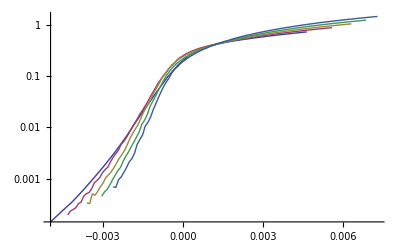

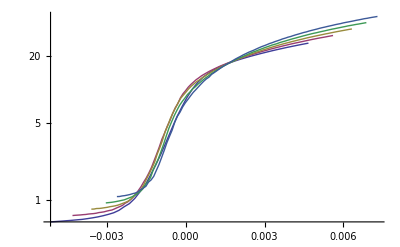

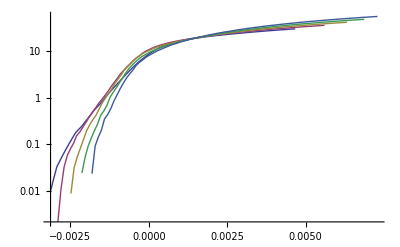

```mathematica
ListLogPlot[{inputg[5],inputg[10],inputg[20],inputg[40],inputg[80]},Joined->True]
ListLogPlot[{inputvar[5],inputvar[10],inputvar[20],inputvar[40],inputvar[80]},Joined->True]
ListLogPlot[{inputvardif[5],inputvardif[10],inputvardif[20],inputvardif[40],inputvardif[80]},Joined->True]
```

-Graphics-

-Graphics-

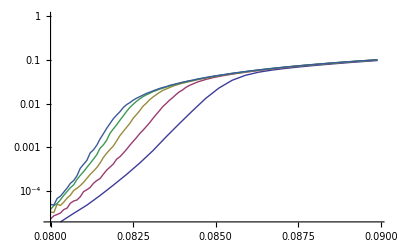

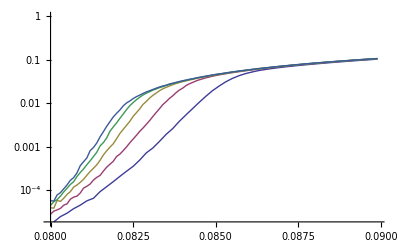

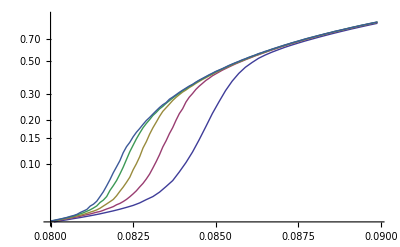

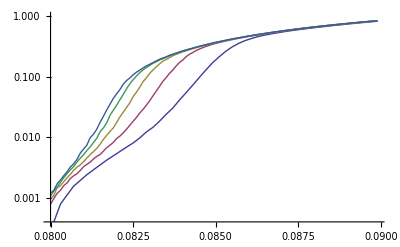

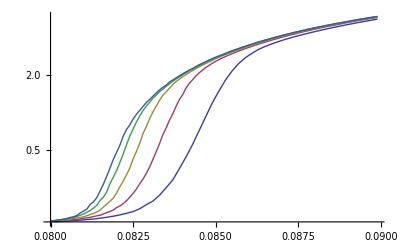

```mathematica
ListPlot[{Gap[v][5],Gap[v][10],Gap[v][20],Gap[v][40],Gap[v][80]},Joined->True]
ListPlot[{AVVar[v][5],AVVar[v][10],AVVar[v][20],AVVar[v][40],AVVar[v][80]},Joined->True]
ListLogPlot[{Gap[v][5],Gap[v][10],Gap[v][20],Gap[v][40],Gap[v][80]},Joined->True]
ListLogPlot[{Vel[v][5],Vel[v][10],Vel[v][20],Vel[v][40],Vel[v][80]},Joined->True]
ListLogPlot[{AVeldif0[v][5],AVeldif0[v][10],AVeldif0[v][20],AVeldif0[v][40],AVeldif0[v][80]},Joined->True]
ListLogPlot[{AVeldif[v][5],AVeldif[v][10],AVeldif[v][20],AVeldif[v][40],AVeldif[v][80]},Joined->True]
ListLogPlot[{AVVar[v][5],AVVar[v][10],AVVar[v][20],AVVar[v][40],AVVar[v][80]},Joined->True]
```

```mathematica
p1=p(1-p)
α=p(1-p)/(1/d-v-1/2)
```

0.09

0.09/(-19/2+1/d)

```mathematica
x=(v-3)*(α*p^2)+(v-2)*(α*p1+(1-α)p^2)+(v-1)*(α(1-p)+(1-α)p1)+v(1-α)(1-p)
```

8.1 (1-0.09/(-19/2+1/d))+7 (0.01 (1-0.09/(-19/2+1/d))+0.0081/(-19/2+1/d))+8 (0.09 (1-0.09/(-19/2+1/d))+0.081/(-19/2+1/d))+0.0054/(-19/2+1/d)

```mathematica
d=0.08
x
```

0.08

8.86

```mathematica
(v-3)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p^2)+(v-2)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)*p(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p^2)+(v-1)*(p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2)(1-p)+(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))p(1-p))+v(1-p(1-p)/(1/AVel[v][l][[All,1]][[i]]-v-1/2))(1-p)
```

```mathematica
ListPlot[{AVeldif[v][5],AVeldif[v][10],AVeldif[v][20],AVeldif[v][40],AVeldif[v][80]},Joined->True]
```

-Graphics-

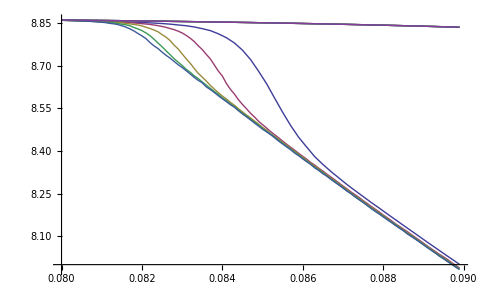

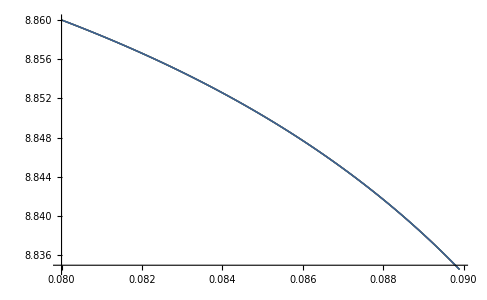

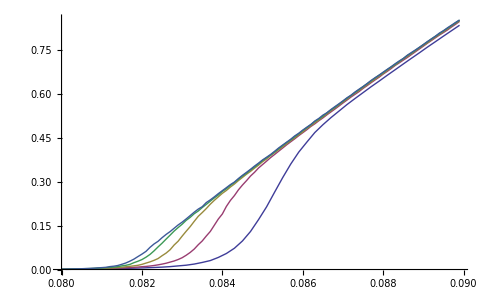

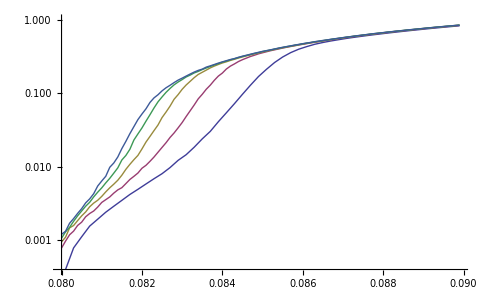

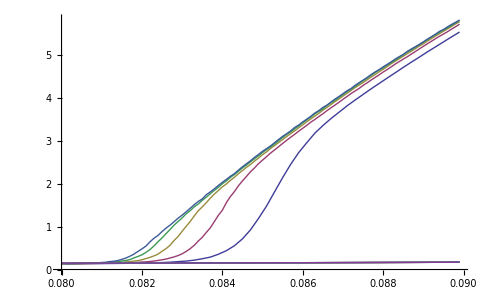

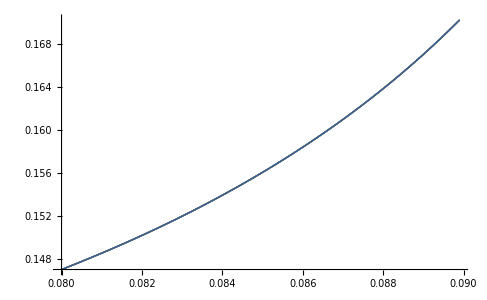

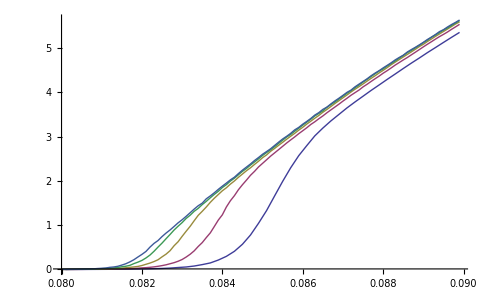

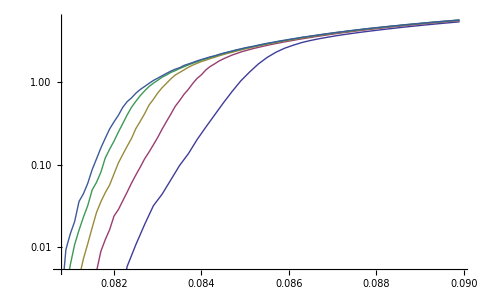

```mathematica
ListPlot[{AVel[v][5],AVel[v][10],AVel[v][20],AVel[v][40],AVel[v][80],sVel[v][5],sVel[v][10],sVel[v][20],sVel[v][40],sVel[v][80]},Joined->True]
ListPlot[{sVel[v][5],sVel[v][10],sVel[v][20],sVel[v][40],sVel[v][80]},Joined->True]
ListPlot[{AVeldif[v][5],AVeldif[v][10],AVeldif[v][20],AVeldif[v][40],AVeldif[v][80]},Joined->True]
ListLogPlot[{AVeldif[v][5],AVeldif[v][10],AVeldif[v][20],AVeldif[v][40],AVeldif[v][80]},Joined->True]
ListPlot[{AVVar[v][5],AVVar[v][10],AVVar[v][20],AVVar[v][40],AVVar[v][80],sVar[v][5],sVar[v][10],sVar[v][20],sVar[v][40],sVar[v][80]},Joined->True]
ListPlot[{sVar[v][5],sVar[v][10],sVar[v][20],sVar[v][40],sVar[v][80]},Joined->True]
ListPlot[{Vardif[v][5],Vardif[v][10],Vardif[v][20],Vardif[v][40],Vardif[v][80]},Joined->True]
ListLogPlot[{Vardif[v][5],Vardif[v][10],Vardif[v][20],Vardif[v][40],Vardif[v][80]},Joined->True]
```

```mathematica
zvardif=0.15
```

0.15

```mathematica
l1=5;
l2=10;
l3=20;
l4=80;
l5=40;
Do[

inputg[l]=Table[{(Gap[v][l][[All,1]][[i]]-(kg+cg*(l*1000)^(exg)))*(l*1000)^zg,Gap[v][l][[All,2]][[i]]*(l*1000)^(-ag)},{i,1,Length[Gap[v][l]]}];
inputv[l]=Table[{(Vel[v][l][[All,1]][[i]]-(kv+cv*(l*1000)^(exv)))*(l*1000)^zv,Vel[v][l][[All,2]][[i]]*(l*1000)^(-av)},{i,1,Length[Vel[v][l]]}];
inputav[l]=Table[{(AVel[v][l][[All,1]][[i]]-(kav+cav*(l*1000)^(exav)))*(l*1000)^zav,AVel[v][l][[All,2]][[i]]*(l*1000)^(-aav)},{i,1,Length[AVel[v][l]]}];
inputavdif0[l]=Table[{(AVeldif0[v][l][[All,1]][[i]]-(kavdif0+cavdif0*(l*1000)^(exavdif0)))*(l*1000)^zavdif0,AVeldif0[v][l][[All,2]][[i]]*(l*1000)^(-aavdif0)},{i,1,Length[AVeldif0[v][l]]}];
inputavdif[l]=Table[{(AVeldif[v][l][[All,1]][[i]]-(kavdif+cavdif*(l*1000)^(exavdif)))*(l*1000)^zavdif,AVeldif[v][l][[All,2]][[i]]*(l*1000)^(-aavdif)},{i,1,Length[AVeldif[v][l]]}];
inputvar[l]=Table[{(AVVar[v][l][[All,1]][[i]]-(kvar+cvar*(l*1000)^(exvar)))*(l*1000)^zvar,AVVar[v][l][[All,2]][[i]]*(l*1000)^(-avar)},{i,1,Length[AVVar[v][l]]}];
inputvardif[l]=Table[{(Vardif[v][l][[All,1]][[i]]-(kvardif+cvardif*(l*1000)^(exvardif)))*(l*1000)^zvardif,Vardif[v][l][[All,2]][[i]]*(l*1000)^(-avardif)},{i,1,Length[Vardif[v][l]]}];
,{l,{l1,l2,l3,l4,l5}}]
```

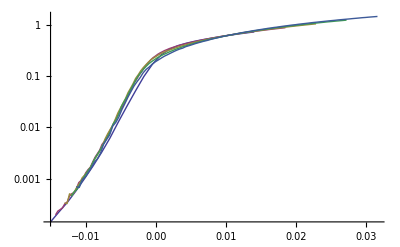

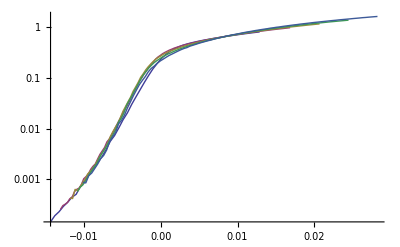

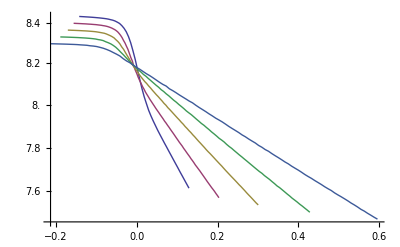

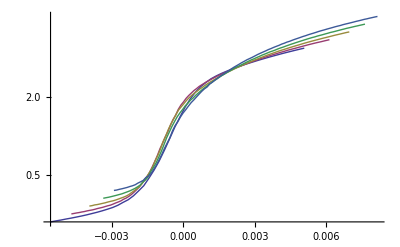

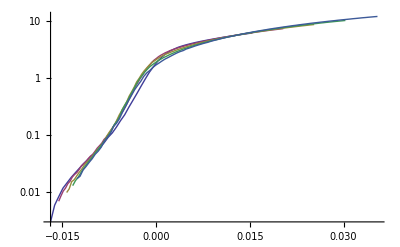

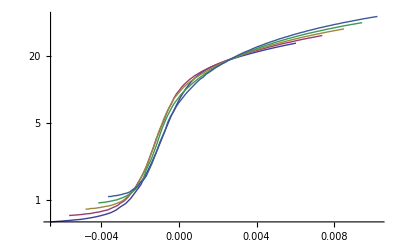

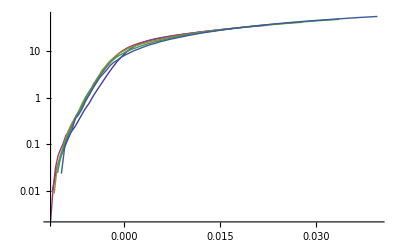

```mathematica
ListLogPlot[{inputg[5],inputg[10],inputg[20],inputg[40],inputg[80]},Joined->True]
ListLogPlot[{inputv[5],inputv[10],inputv[20],inputv[40],inputv[80]},Joined->True]
ListLogPlot[{inputav[5],inputav[10],inputav[20],inputav[40],inputav[80]},Joined->True]
ListLogPlot[{inputavdif0[5],inputavdif0[10],inputavdif0[20],inputavdif0[40],inputavdif0[80]},Joined->True]
ListLogPlot[{inputavdif[5],inputavdif[10],inputavdif[20],inputavdif[40],inputavdif[80]},Joined->True]
ListLogPlot[{inputvar[5],inputvar[10],inputvar[20],inputvar[40],inputvar[80]},Joined->True]
ListLogPlot[{inputvardif[5],inputvardif[10],inputvardif[20],inputvardif[40],inputvardif[80]},Joined->True]
```

```mathematica
" = cg" cg
" = cv" cv
" = cav (off)"cav
" = cavdif0 (off)" cavdif0
" = cavdif" cavdif
" = cvar (off)" cvar
" = cvardif" cvardif
"-------------"
" = exg" exg
" = exv" exv
" = exav (off)"exav
" = exavdif0 (off)" exavdif0
" = exavdif" exavdif
" = exvar (off)" exvar
" = exvardif" exvardif
"-------------"
" = zg" zg
" = zv" zv
" = zav (off)"zav
" = zavdif0 (off)" zavdif0
" = zavdif" zavdif
" = zvar (off)" zvar
" = zvardif" zvardif
"-------------"
" = ag" ag
" = av" av
" = aav (off)"aav
" = aavdif0 (off)" aavdif0
" = aavdif" aavdif
" = avar (off)" avar
" = avardif" avardif
```

0.1056  = cg

0.1056  = cv

0.104276  = cav (off)

0.104276  = cavdif0 (off)

0.104276  = cavdif

0.104276  = cvar (off)

0.104276  = cvardif

-------------

-0.382985  = exg

-0.382985  = exv

-0.382532  = exav (off)

-0.382532  = exavdif0 (off)

-0.382532  = exavdif

-0.382532  = exvar (off)

-0.382532  = exvardif

-------------

0.13  = zg

0.12  = zv

0.39  = zav (off)

0.01  = zavdif0 (off)

0.14  = zavdif

0.03  = zvar (off)

0.15  = zvardif

-------------

-0.235594  = ag

-0.241176  = av

0.00581585  = aav (off)

-0.196563  = aavdif0 (off)

-0.233128  = aavdif

-0.182465  = avar (off)

-0.202216  = avardif